How Quantum Decoherence Occurs |

Double-Slit Interferencepaclet:Q3/tutorial/HowQuantumDecoherenceOccurs#433762024 | Complete Decoherencepaclet:Q3/tutorial/HowQuantumDecoherenceOccurs#1763954588
Mach-Zehnder Interferencepaclet:Q3/tutorial/HowQuantumDecoherenceOccurs#584647518 | Partial Decoherencepaclet:Q3/tutorial/HowQuantumDecoherenceOccurs#226170303

See also Section 5.1 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

Let us take a toy model and its variants to examine how a quantum state loses phase coherence. As one will see, those models are oversimplifications. Nevertheless, they are sufficient to inspire a qualitative physical picture of decoherence. They provide motivations and elementary examples for more rigorous mathematical frameworks.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Double-Slit Interference

The phase coherence of quantum states can be seen best in interference experiments. The most popular interference experiment is the double-slit experiment in Figure 1 (a). Ranked top in a survey (Crease, 2002) about “the most beautiful experiment in physics,” the double-slit experiment with electrons (Jönsson, 1961) played a decisive role to establish de Broglie’s wave-particle duality for any particle in quantum physics. Notably, in a later experiment (Tonomura et al., 1989), there was only one electron in the apparatus at any one time. This was one of the thought experiment that Feynman (Feynman et al., 1963) suggested emphasizing the coherent nature of the quantum state. In Dirac’s words (Dirac, 1958), “each [electron] interferes only with itself.”

Feynman’s other thought experiment (Feynman et al., 1963) illustrated in Figure 1 (b) is an interesting variant of the double-slit experiment in the present context. In this experiment, a particle detector located at the upper slit can determine which slit each electron passes through. The so-called which-path information breaks the interference pattern and one can observe no interference fringe. A common explanation of the disappearance of interference in this experiment is based on the principle of complementarity. In quantum mechanics, anything has both the wave and particle nature but exhibits only one of them exclusively at a time (in a given situation). Indeed, the experiment is essentially the same as the thought experiment suggested by Einstein in a discussion with Bohr at the Fifth Physical Conference of the Solvay Institute, devoted to “Electrons and Photons” (Bohr, 1949), in 1927. Bohr gave the same argument. However, a closer analysis of the thought experiment also reveals the physical mechanism of decoherence. Here we will focus on this point.

-Graphics--Graphics-

Figure 1. Double-slit experiments with single electrons. (a) The number density of electrons accumulated on the screen exhibits a clear interference pattern. (b) A particle detector (gray disk) is located at the upper slit. In this case, no interference pattern is observed.

Mach-Zehnder Interference

```mathematica
<<Q3`
Let[Qubit,S]
```

To make the point clearer, it is convenient to consider a slightly different version with the Mach-Zehnder interferometer in Figure 2. In Figure 2 (left), a photon is incident on the horizontal optical mode (the lower blue arm of the interferometer) and encounters a beam splitter. It can either go through the beam splitter to the other side of the horizontal mode or reflected into the vertical mode (the upper red arm). The photon after the beam splitter is thus in the state of superposition (0+1)/√2, where |0⟩ and |1⟩ describe the photon in the blue and red arms, respectively. In the blue arm, the photon passes through an optical medium that causes an additional phase shift of ϕ. The state of the photon in this stage is given by (0+1 ⅇ^(ⅈ ϕ))/√2. The two arms are recombined at the second beam splitter, where the photon is either transmitted or reflected. The photon is then described by the state

0((1+ⅇ^(ⅈ ϕ))/2)+1((1-ⅇ^(ⅈ ϕ))/2) ,

where the additional phase factor of −1 (phase shift by π) for a photon reflected from the red to blue arm is responsible for the reflection from an optically hard medium. The photon is finally detected by either detectors at the ends of the optical modes. The probability to detect the photon in the blue arm is given by

P_0=(|(1+ⅇ^(ⅈ ϕ))/2|)^2=cos^2(ϕ/2) .

Similarly, the probability to find the photon in the red arm is given by

P_1=sin^2(ϕ/2) .

Clearly, the photon detection probability in each output port manifests interference as the relative phase shift ϕ varies. As the analyses of the photon states in respective stages suggest, the Mach-Zehnder interferometer in Figure 2 (left) for a photon is an equivalent of the quantum circuit in Figure 3 (left) for a qubit.

-Graphics--Graphics-

Figure 2. Mach-Zehnder interference experiments. (left) Ideal case without decoherence. The region labeled with ϕ causes a relative phase shift in the photon traveling along the upper arm. (right) The photon traveling along the upper arm interacts with a two-level system and causes it to make a transition from the ground state ϵ_0 to the excited state ϵ_1.

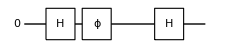
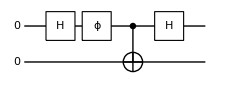

Figure 3. Quantum circuits equivalent to the Mach-Zehnder interference experiments in Figure 2. The Hadamard gate is the equivalent of the beam splitter in the Mach-Zehnder interferometer while the additional qubit corresponds to the two-level system coupled to the upper optical mode and the CNOT gate simulates the coupling. The unitary gate labeled by ϕ is the phase gate, 00+1 ⅇ^(ⅈ ϕ)1.

For demonstration, consider a quantum circuit model equivalent to the Mach-Zehnder interferometer.

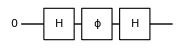

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S[1]],S[1,6],Phase[ϕ,S[1],"Label"->"ϕ"],S[1,6]]
```

```mathematica
out=Elaborate[qc];
out//LogicalForm
```

1/2 (1+ⅇ^(ⅈ ϕ)) 0_S_1+1/2 (1-ⅇ^(ⅈ ϕ)) 1_S_1

```mathematica
Let[Real,ϕ]
{P[0,ϕ_],P[1,ϕ_]}=Abs[Normal@Matrix@out]^2//Elaborate//ExpToTrig//Simplify
```

{Cos[ϕ/2]^2,Sin[ϕ/2]^2}

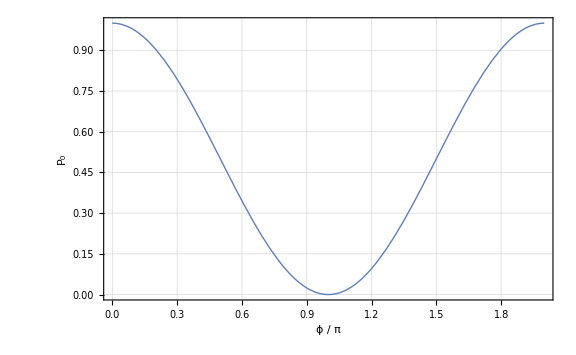

```mathematica
Plot[P[0,Pi s],{s,0,2},FrameLabel->{"ϕ / π","P_0"}]
```

Complete Decoherence

```mathematica
<<Q3`
Let[Qubit,S]
```

Let us now consider a variant in Figure 2 (right). In this experiment, there is a two-level system coupled to the upper optical mode. In other words, if the photon is in the red arm, then it interacts with a two-level system. As a result of the interaction, the two-level system, which is initially prepared in its ground state ϵ_0, makes a transition to the excited state ϵ_1. The two-level system is the counterpart of the particle detector behind the upper slit in the double-slit experiment in Figure 1 (b). Here we will regard it as an environment. The crucial point is that unlike the particle detector, one cannot assess the two-level system in this experiment. Nevertheless, through the interaction with the photon traveling in the upper arm, the two-level system destroys the interference.

To see this, let us take a closer look at what happens in the experiment. The initial state of the total system consisting of the incident photon and the two-level system is 0⊗ϵ_0. After the beam splitter and the phase-shifter medium, it becomes

((0+1 ⅇ^(ⅈ ϕ))/(√2))⊗ϵ_0=(0⊗ϵ_0+1⊗ϵ_0 ⅇ^(ⅈ ϕ))/(√2)

The interaction between the photon and the two-level system causes the transition from ϵ_0 to ϵ_1 on the condition that the photon is in the upper arm. It leads to

(0⊗ϵ_0+1⊗ϵ_1 ⅇ^(ⅈ ϕ))/(√2)

for the state of the total system. The process is analogous to the CNOT gate in quantum computation. Indeed, the Mach-Zehnder experiment in Figure 2 (right) with a two-level system coupled to one of the optical mode is equivalent to the quantum circuit in Figure 3 (right) for two qubits. After the second beam splitter, the quantum state is described by

0⊗((ϵ_0+ϵ_1 ⅇ^(ⅈ ϕ))/2)+1⊗((ϵ_0-ϵ_1 ⅇ^(ⅈ ϕ))/2) .

The probability to detect the photon at the output port of the blue arm is thus given by

P_0=1/4(ϵ_0+ⅇ^(-ⅈ ϕ)ϵ_1)(ϵ_0+ϵ_1 ⅇ^(ⅈ ϕ))=1/2 .

Likewise, the probability to detect the photon in the other arm is

P_1=1/2 .

Whence the photon detection probabilities show no interference effect.

It is worth noting that the final quantum state is a maximally entangled state between the photon and the two-level system (the maximal entanglement is even clearer in the quantum state before the second beam splitter). This means that upon tracing out the two-level system, which we cannot assess, the density operator describing the quantum state of the photon becomes completely random, ρ = I/2, irrespective of the relative phase shift ϕ. That is, due to the interaction and subsequent entanglement with the two-level system, the photon has lost completely the phase coherence in its quantum state.

For demonstration, consider a quantum circuit model equivalent to the Mach-Zehnder interference experiment with a two-level system coupled to one of the two arms.

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],Phase[ϕ,S[1],"Label"->"ϕ"],CNOT[S[1],S[2]],S[1,6]]
```

-Graphics-

```mathematica
out=Elaborate[qc];
out//LogicalForm
```

1/2 0_S_10_S_2+1/2 ⅇ^(ⅈ ϕ) 0_S_11_S_2+1/2 1_S_10_S_2-1/2 ⅇ^(ⅈ ϕ) 1_S_11_S_2

```mathematica
Let[Real,ϕ]
rho=PartialTrace[out,S[2]]
```

1/2

Partial Decoherence

```mathematica
<<Q3`
Let[Qubit,S]
```

In Feynman’s thought experiment in Figure 1 (b), it has been assumed that the particle detector behind the upper slit is perfect. In the Mach-Zehnder version in Figure 2 (right), it corresponds to an interaction between the photon and the two-level system such that the quantum state ϵ_1 of the two-level system after the interaction is orthogonal to the initial state ϵ_0. Recall that in principle one can devise a measurement to discriminate two orthogonal states with certainty.

What if the detector is not perfect? For example, suppose that the detector efficiency is so low that it often misses the particle even if it passes through the upper slit. How much would the presence of such a detector affect, if at all, the interference pattern in the screen? Translated to the Mach-Zehnder experiment in Figure 2 (right), it corresponds to a quantum state, now denoted by ϵ'_1 to be distinguished from ϵ_1, of the two-level system after the interaction with the photon is not orthogonal to ϵ_0. It is also analogous to the quantum circuit

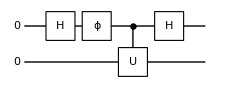

where the unitary gate U is responsible for the transition ϵ_0→ϵ'_1, that is, ϵ'_1=Uϵ_0.

Following the above lines of argument, one can obtain the final state of the combined system of the photon and the two-level system as

0⊗((ϵ_0+ϵ'_1 ⅇ^(ⅈ ϕ))/2)+1⊗((ϵ_0-ϵ'_1 ⅇ^(ⅈ ϕ))/2) .

which is to be compared to the previous final state. The photon detection probabilities are given by

P_0=1/4(ϵ_0+ⅇ^(-ⅈ ϕ)ϵ'_1)(ϵ_0+ϵ'_1 ⅇ^(ⅈ ϕ))=1/2(1+Reϵ_0ϵ'_1 ⅇ^(ⅈ ϕ)) ,

P_1=1/4(ϵ_0-ⅇ^(-ⅈ ϕ)ϵ'_1)(ϵ_0-ϵ'_1 ⅇ^(ⅈ ϕ))=1/2(1-Reϵ_0ϵ'_1 ⅇ^(ⅈ ϕ)) .

Clearly, when ϵ'_1 is orthogonal to ϵ_0, ϵ_0ϵ'_1=0, the previous results are reproduced, and one can observe no interference. Furthermore, when there is no interaction between the photon and the two-level system, the two-level system should remain in the initial state ϵ_0, ϵ'_1=ϵ_0. In this case, the photon detection probabilities recover interference to the full extent. The above result  shows that in general, the interference is destroyed only partially depending on how easy ϵ'_1 can be, in principle, discriminated from ϵ_0. Putting it another way, the better the environment “knows” about the quantum state, the more loss of phase coherence it suffers.

For demonstration, now consider a quantum circuit model equivalent to the Mach-Zehnder interference experiment with a two-level system weakly coupled to one of the two arms. Here we assume the unitary operator U=U_y(θ) with θ<π acting conditionally on the two-level system.

```mathematica
qc=QuantumCircuit[LogicalForm[Ket[],S@{1,2}],S[1,6],Phase[ϕ,S[1],"Label"->"ϕ"],ControlledU[S[1],Rotation[θ,S[2,2]],"Label"->"U"],S[1,6]]
```

-Graphics-

The final state is an entangled state in general.

```mathematica
out=Elaborate[qc]//Simplify;
out//LogicalForm
```

1/2 ((1+ⅇ^(ⅈ ϕ) Cos[θ/2]) 0_S_10_S_2+(1-ⅇ^(ⅈ ϕ) Cos[θ/2]) 1_S_10_S_2-ⅇ^(ⅈ ϕ) (-0_S_11_S_2+1_S_11_S_2) Sin[θ/2])

However, the entanglement is not a maximally entangled state. The density operator for the photon manifests coherence to certain extent.

```mathematica
Let[Real,ϕ,θ]
rho=PartialTrace[out,S[2]]//ExpToTrig//Elaborate
```

1/2+1/2 Cos[θ/2] Cos[ϕ] S_1^z-1/2 Cos[θ/2] S_1^y Sin[ϕ]

```mathematica
{P[0,θ_,ϕ_],P[1,θ_,ϕ_]}=Diagonal@Matrix@rho
```

{1/2+1/2 Cos[θ/2] Cos[ϕ],1/2-1/2 Cos[θ/2] Cos[ϕ]}

Depending on the strength of the coupling, the interference may survive partially.

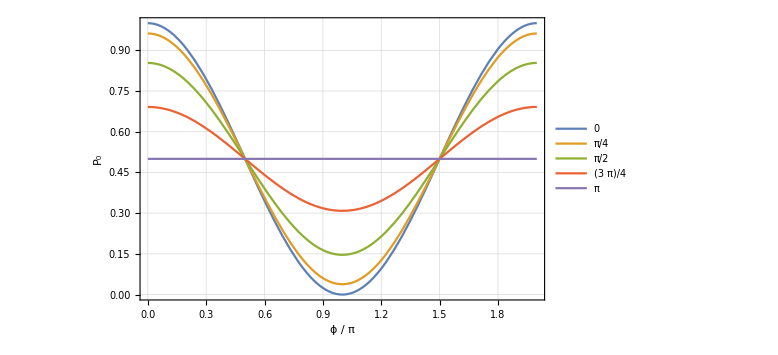

```mathematica
tt=Range[0,4]Pi/4;
Plot[Evaluate[P[0,#,Pi s]&/@tt],{s,0,2},
FrameLabel->{"ϕ / π","P_0"},PlotLegends->tt]
```

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Noise and Decoherence
▪Quantum Information Systems with Q3

| Related Links
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).